1. С помощью интерполяционного полинома Лагранжа вычислить производную функции. Сравнить с результатом вычисления с помощью встроенной функции InterpolatingPolynomial и с помощью встроенной функции D.

6. f(x)=5^x+∫_0^x (cos(t))/(1+t^2)ⅆt;x_0=1.1, x_1=1.4, x_2=1.7, x_3=2. Найти f''(1.5).

Интерполяционный полином Лагранжа:

-40.6156 (-2+x$3562935) (-1.7+x$3562935) (-1.4+x$3562935)+190.049 (-2+x$3562935) (-1.7+x$3562935) (-1.1+x$3562935)-299.494 (-2+x$3562935) (-1.4+x$3562935) (-1.1+x$3562935)+158.818 (-1.7+x$3562935) (-1.4+x$3562935) (-1.1+x$3562935)

Производная 2 порядка интерполяционного полинома Лагранжа:

-300.121 (-2+x$3563096)+616.503 (-1.7+x$3563096)-362.582 (-1.4+x$3563096)+98.7468 (-1.1+x$3563096)

Производная 2 порядка интерполяционного полинома Лагранжа в точке х=1.5:

30.0002

InterpolatingPolynomial:

25.7285+(21.2765+(17.6274+8.7578 (-1.7+x)) (-1.1+x)) (-2+x)

Производная:

35.2549+17.5156 (-2+x)+17.5156 (-1.7+x)+17.5156 (-1.1+x)

InterpolatingPolynomial''[{{1.1,6.57973},{1.4,10.2626},{1.7,16.1727},{2,25.7285}},x]

Вторая производная в точке 1,5, полученная методом InterpolatingPolynomial:

30.0002

Результаты совпадают.

Вторая производная в точке 1,5, полученная методом D:

NIntegrate::nlim: s = x is not a valid limit of integration.

-(2 x Cos[x])/((1+x^2)^2)+5^x Log[5]^2-Sin[x]/(1+x^2)

28.6333

Построить аппроксимацию Паде.

NIntegrate::nlim: s = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

(6.57973+13.2653 (-1.1+x)+12.6763 (-1.1+x)^2+7.11751 (-1.1+x)^3+2.5239 (-1.1+x)^4+0.517688 (-1.1+x)^5)/(1+0.548295 (-1.1+x)+0.0119145 (-1.1+x)^2-0.185233 (-1.1+x)^3+0.0437638 (-1.1+x)^4)

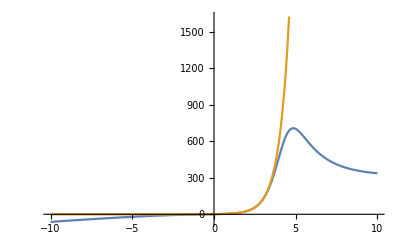

```mathematica
Style[Text["1. С помощью интерполяционного полинома Лагранжа вычислить производную функции. Сравнить с результатом вычисления с помощью встроенной функции InterpolatingPolynomial и с помощью встроенной функции D."],FontSize->25]
Text["6. f(x)=5^x+∫_0^x (cos(t))/(1+t^2)ⅆt;x_0=1.1, x_1=1.4, x_2=1.7, x_3=2. :041d:0430:0439:0442:0438 f''(1.5)."]
f[x_]:=5^x+NIntegrate[Cos[s]/(1+s^2),{s,0,x},PrecisionGoal->10]


getPolynom[]:=Module[
{i,j,x,xs,s,f,L},
xs={1.1,1.4,1.7,2};
f[x_]:=5^x+NIntegrate[Cos[s]/(1+s^2),{s,0,x}];
L[x_]:=f[xs[[1]]]*(((x-xs[[2]])*(x-xs[[3]])*(x-xs[[4]]))/((xs[[1]]-xs[[2]])*(xs[[1]]-xs[[3]])*(xs[[1]]-xs[[4]]))) + f[xs[[2]]]*(((x-xs[[1]])*(x-xs[[3]])*(x-xs[[4]]))/((xs[[2]]-xs[[1]])*(xs[[2]]-xs[[3]])*(xs[[2]]-xs[[4]]))) + f[xs[[3]]]*(((x-xs[[1]])*(x-xs[[2]])*(x-xs[[4]]))/((xs[[3]]-xs[[1]])*(xs[[3]]-xs[[2]])*(xs[[3]]-xs[[4]]))) + f[xs[[4]]]*(((x-xs[[1]])*(x-xs[[2]])*(x-xs[[3]]))/((xs[[4]]-xs[[1]])*(xs[[4]]-xs[[2]])*(xs[[4]]-xs[[3]])));
Print[L[x]];
];
getDeriv[]:=Module[ {x0,x,xs,f,L,s},
x0=1.5;
xs={1.1,1.4,1.7,2};
f[x_]:=5^x+NIntegrate[Cos[s]/(1+s^2),{s,0,x}];
L[x_]:=f[xs[[1]]]*(((x-xs[[2]])*(x-xs[[3]])*(x-xs[[4]]))/((xs[[1]]-xs[[2]])*(xs[[1]]-xs[[3]])*(xs[[1]]-xs[[4]]))) + f[xs[[2]]]*(((x-xs[[1]])*(x-xs[[3]])*(x-xs[[4]]))/((xs[[2]]-xs[[1]])*(xs[[2]]-xs[[3]])*(xs[[2]]-xs[[4]]))) + f[xs[[3]]]*(((x-xs[[1]])*(x-xs[[2]])*(x-xs[[4]]))/((xs[[3]]-xs[[1]])*(xs[[3]]-xs[[2]])*(xs[[3]]-xs[[4]]))) + f[xs[[4]]]*(((x-xs[[1]])*(x-xs[[2]])*(x-xs[[3]]))/((xs[[4]]-xs[[1]])*(xs[[4]]-xs[[2]])*(xs[[4]]-xs[[3]])));
Print["Производная 2 порядка интерполяционного полинома Лагранжа: "];
Print[L''[x]];
Print["Производная 2 порядка интерполяционного полинома Лагранжа в точке х=1.5: "];
Print[L''[x0]]
];

getPade[f_,{x_,x0_,{m_,n_}}]:=Module[{a,b,c,row,pade,num,denom},
num=Sum[a[k]*x^k,{k,0,5}];
denom=1+Sum[b[k]*x^k,{k,1,4}];
pade = num/denom;
row = Normal@Series[f[x],{x,0,m+n}];
num/denom==row;
num-denom*row==0;
(num-denom*row==0)//Collect[#,x]&;
leftPart = CoefficientList[num-denom*row,x];
system=(#==0&)/@leftPart;
coeffs=CoefficientList[#,x]&/@{num,denom}//Flatten;
coeffs=DeleteCases[coeffs,_?NumericQ];
solution = Solve[system[[;;Length@coeffs]],coeffs];
pade = pade/.solution[[1]];
Return[pade];
];

getPadeNew[f_,{x_,x0_,{m_,n_}}]:=Module[
{coeffs=Table[0,0], 
i=1,
rowSum = 0, 
row=Series[f[x],{x,x0,m+n}], 
z, padeApprox =0},
For[i,i≤m+n+1, i++,
rowSum= SeriesCoefficient[row, i-1]+Sum[SeriesCoefficient[row, i-k-1] b[k],{k, 1, i-1}];
AppendTo[coeffs,rowSum==a[i-1]];
];
z=Join[Array[a[#]->0&,n,{m+1, m+n}], Array[b[#]->0&,m , {n+1, m+n}]];
coeffs=coeffs/.z;
solution=NSolve[coeffs, Join[Array[a[#]&,m+1,{0,m}], Array[b[#]&, n, {1, n}]]];
padeApprox = Sum[a[k] (x-x0)^(k), {k, 0,m}]/ (1+Sum[b[k] (x-x0)^(k), {k, 1,n}])/.solution;
Return[padeApprox[[1]]];
];

Text["Интерполяционный полином Лагранжа: "]
getPolynom[]
getDeriv[]
Text["InterpolatingPolynomial: "]
Clear[s,L]
InterpolatingPolynomial[{{1.1,f[1.1]},{1.4,f[1.4]},{1.7,f[1.7]},{2,f[2]}},x]
Text["Производная: "]
D[D[InterpolatingPolynomial[{{1.1,f[1.1]},{1.4,f[1.4]},{1.7,f[1.7]},{2,f[2]}},x],x],x]
Text["Вторая производная в точке 1,5, полученная методом InterpolatingPolynomial: "]
35.25485614193585+17.51560974177413*(-2+1.5)+17.51560974177413*(-1.7+1.5)+17.51560974177413*(-1.1+1.5)
Text["Результаты совпадают."]
Text["Вторая производная в точке 1,5, полученная методом D: "]
D[D[f[x],x],x]
-(2 *1.5*Cos[1.5])/((1+1.5^2)^2)+5^1.5 Log[5]^2-Sin[1.5]/(1+1.5^2)
Style[Text["Построить аппроксимацию Паде."],FontSize->25]
pade=getPadeNew[f,{x,1.1,{5,4}}]
Plot[{pade, f[x]}, {x, -10,10}]
```